```mathematica
(* Flow deflection around Europa's Alfven wings, start: 11/21/20 *)

(*-------------------------------------------*)
(*Basic Input Parameters*)
(*-------------------------------------------*)
```

```mathematica
RE= 1560.8 * 10^3;
B0= 450 * 10^-9; (*background magnetic field, southward, center of plasma sheet, from Arnold2020a*)
n0=60 * 10^6; (*upstream number density, from Arnold2020, table 1*)
u0=100*10^3; (*upstream flow velocity 100 km/s, from Arnold2020b *)
E0=u0*B0; (*MAGNITUDE OF convective electric field*)
mp=1.6726231*10^-27; (*proton mass*)
m=18.5 * mp; (*upstream ion mass, from Arnold2020b*)
SigmaP= 30 ;(*exospheric Pedersen conductance, from table 21.1, page 517, Kivelson2004*)
H= 100 * 10^3; (*exospheric scale height, from Arnold2020b*)
mu0= 4 * 3.14159265359* 10^-7 ;(*magnetic permeability of vacuum*)
```

```mathematica
(*-------------------------------------------*)
(*Derived parameters for Alfven wing*)
(*-------------------------------------------*)
vA=B0/(√(mu0 * n0 * m)); (*Alfven velocity*)
MA= u0/vA; (*Alfvenic Mach number*)
SigmaA=1/(mu0 * vA*√(1+MA^2)); (*Alfven conductance, Equation (5) in Simon2011*)
```

```mathematica
(*-------------------------------------------*)
(*Exospheric conductance profile*)
(*-------------------------------------------*)
```

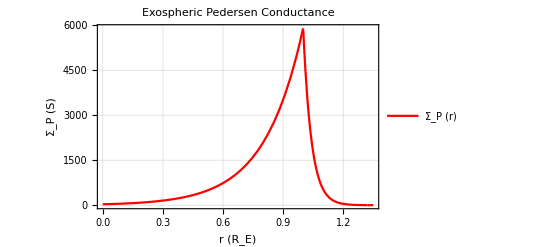

```mathematica
r[x_,y_] = √(x^2+ y^2); (*radial distance from z axis in cylindrical coordinates, NOT radial distance to Europa's surface, (x,y) dependency NOT needed for merely plotting the exospheric conductance profile*)
R1= RE ;(*radial boundary of the Europa fluxtube, x^2+y^2 = RE^2*)
R2=  RE+ 5 H;(*outer boundary of region with non-zero transverse conductance, assumimng the atmosphere "ends" at a distance of 5 scale heights. exp(-5)=0.00674*)
beta = 1/(3H) ;(*given input parameter for conductance profile, using some multiple of the exospheric scale height H here*)
Sigma1[r_]= (SigmaP+SigmaA)* Exp[beta* r]-SigmaA; (*Pedersen conductance within the Europa fluxtube r < R1*)
Sigma2[r_]= SigmaA *Exp[(Log[(SigmaP+SigmaA)/SigmaA]+ beta * R1)/(R2-R1)*(R2-r)]-SigmaA;
(*Pedersen conductance outside the Europa fluxtube, but within the exosphere R1 < r < R2*)
Sigma3[r_]= 0 ; (*Pedersen conductance outside of Europa fluxtube, R2 < r*)
SigmaExo[r_]= Piecewise[{{Sigma1[r], r ≤ R1},{Sigma2[r], R1 < r ≤ R2},{Sigma3[r], R2 < r}}];
(*putting all three segments together*)

(*Plot exopspheric conductance profile*)
Plot[SigmaExo[r*RE],{r,0,1.35}, FrameLabel->{"r (R_E)","Σ_P (S)"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"Exospheric Pedersen Conductance", PlotStyle->{Red,Thick},PlotLegends ->{"Σ_P (r)"}]
```

```mathematica
(*-------------------------------------------*)
(*Solution for the electric potential psi*)
(*-------------------------------------------*)
delta =(Log[(SigmaP+SigmaA)/SigmaA]+ beta * R1)/(R2-R1); (*Exponent of the conductance profile SigmaP= gamma exp(MINUS delta r) for R1 < r < R2*)
```

```mathematica
(*Calculting the constants of integration, same nomenclature as in hand-written notes*)
M={{(beta*R1-1+Exp[-beta* R1])/R1,(delta*R1+1)/R1, (-Exp[delta*R1])/R1,0},{0, -(delta*R2+1)/R2, Exp[delta*R2]/R2,-1/R2},{(1-(beta*R1+1)*Exp[-beta*R1])/R1^2,-1/R1^2, -1/R1^2 Exp[delta*R1] (delta*R1-1) ,0},{0,1/R2^2,(Exp[delta*R2] *(delta*R2-1))/R2^2, 1/R2^2}};
c={{0},{E0*R2},{0},{E0}};
MatrixForm[M];
{{K1},{K3},{K4},{K5}}=Inverse[M].c;
(*Sin phi and Cos phi*)
sinphi[x_,y_]=y/(√(x^2+y^2));
cosphi[x_,y_]=x/(√(x^2+y^2));
(*Solution for the electric potential psi, angle term from equation 19 in Simon2015*)
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.69616×10^-6,0.0000161338,-20351.2,0.},{0.,-0.0000159783,3.566×10^7,-4.85248×10^-7},{3.96484×10^-13,-4.10493×10^-13,-0.302264,0.},{0.,2.35466×10^-13,535.18,2.35466×10^-13}} may contain significant numerical errors.

```mathematica
M.Inverse[M];//MatrixForm ;(*test: M. Inverse[M]= unit matrix*)
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.69616×10^-6,0.0000161338,-20351.2,0.},{0.,-0.0000159783,3.566×10^7,-4.85248×10^-7},{3.96484×10^-13,-4.10493×10^-13,-0.302264,0.},{0.,2.35466×10^-13,535.18,2.35466×10^-13}} may contain significant numerical errors.

```mathematica
psi1[x_,y_]=sinphi[x,y]* (K1*(beta*r[x,y]-1)+K1*Exp[-beta*r[x,y]])/r[x,y];
psi2[x_,y_]=sinphi[x,y]*(-K3*(delta*r[x,y]+1)+K4*Exp[delta*r[x,y]])/r[x,y];
psi3[x_,y_]=sinphi[x,y]*(E0*r[x,y]+K5/r[x,y]);
psi[x_,y_]=Piecewise[{{0,r[x,y]==0},{psi1[x,y],0<r[x,y] ≤ R1},{psi2[x,y],  R1 < r[x,y] ≤ R2},{psi3[x,y], R2< r[x,y] }}];
```

```mathematica
(*Cut through potential along diagonal axis (x,x) , diagnostic plots*)
psialongdiag[x_]=psi[x,x];
```

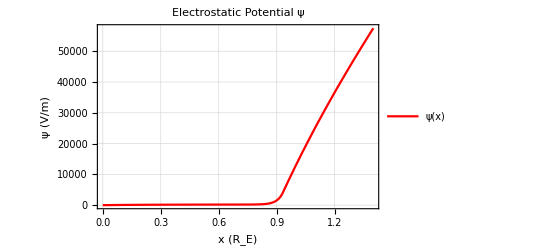

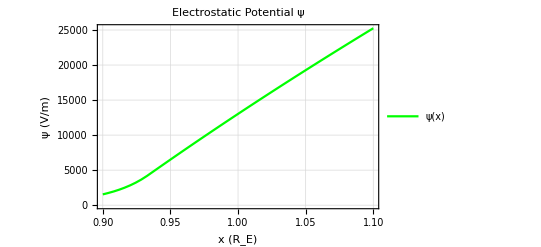

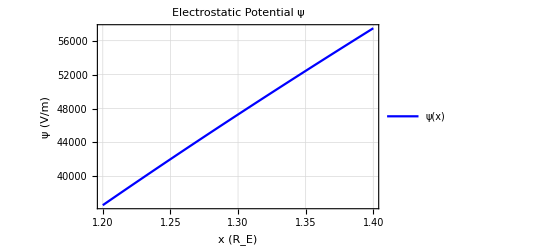

```mathematica
Plot[psialongdiag[x*RE],{x,0,1.4}, FrameLabel->{"x (R_E)","ψ (V/m)"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"Electrostatic Potential ψ", PlotStyle->{Red,Thick},PlotLegends ->{"ψ(x)"}] 
Plot[psialongdiag[x*RE],{x,0.9,1.1}, FrameLabel->{"x (R_E)","ψ (V/m)"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"Electrostatic Potential ψ", PlotStyle->{Green,Thick},PlotLegends ->{"ψ(x)"}] (*visualizes first "kink" at R1=1  RE*)
Plot[psialongdiag[x*RE],{x,1.2,1.4}, FrameLabel->{"x (R_E)","ψ (V/m)"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"Electrostatic Potential ψ", PlotStyle->{Blue,Thick},PlotLegends ->{"ψ(x)"}] 
(*visualizes second "kink", for these tests located at R2=1.3205  RE = RE+5H*)
```

```mathematica
(*Now: verify that for large r= sqrt(2) x, psialongdiag becomes indeed E0 r sin phi = E0 sqrt(2) x * x/sqrt{2}x + E0 x*)
```

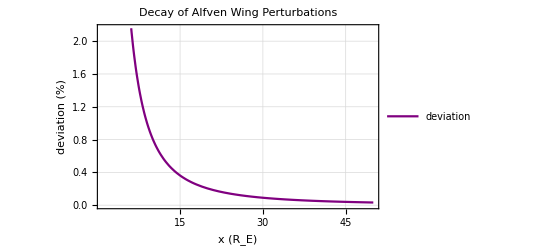

```mathematica
deviation[x_]= Abs[(E0*x-psialongdiag[x])/(E0*x)]*100; (*deviation in percent*)
Plot[deviation[x*RE],{x,1,50}, FrameLabel->{"x (R_E)","deviation (%)"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"Decay of Alfven Wing Perturbations", PlotStyle->{Purple,Thick},PlotLegends ->{"deviation"}]
```

```mathematica
(*-------------------------------------------*)
(*Calculate flow field u near Alfven wings*)
(*-------------------------------------------*)
```

```mathematica
(*first step: need derivatives of the potential psi. Must be implemented with great care, since we encounter a 0/0 situation at r=0 in both cases that mathematica can not handle.*)
dxpsi1[x_,y_]= cosphi[x,y]*sinphi[x,y]*K1*(1-Exp[-beta*r[x,y]]*(beta*r[x,y]+1))/(r[x,y]*r[x,y])- sinphi[x,y]/r[x,y]*cosphi[x,y]*(K1*(beta*r[x,y]-1)+K1*Exp[-beta*r[x,y]])/r[x,y];
dxpsi2[x_,y_]=cosphi[x,y]*sinphi[x,y]*(K3+K4*Exp[delta*r[x,y]]*(delta*r[x,y]-1))/(r[x,y]*r[x,y])- sinphi[x,y]/r[x,y]*cosphi[x,y]*(-K3*(delta*r[x,y]+1)+K4*Exp[delta*r[x,y]])/r[x,y];
dxpsi3[x_,y_]=cosphi[x,y]*sinphi[x,y]*(E0-K5/(r[x,y]*r[x,y]))- sinphi[x,y]/r[x,y]*cosphi[x,y]*(E0*r[x,y]+K5/r[x,y]);
dypsi1[x_,y_]=sinphi[x,y]*sinphi[x,y]*K1*(1-Exp[-beta*r[x,y]]*(beta*r[x,y]+1))/(r[x,y]*r[x,y])+ cosphi[x,y]/r[x,y]*cosphi[x,y]*(K1*(beta*r[x,y]-1)+K1*Exp[-beta*r[x,y]])/r[x,y];
dypsi2[x_,y_]=sinphi[x,y]*sinphi[x,y]*(K3+K4*Exp[delta*r[x,y]]*(delta*r[x,y]-1))/(r[x,y]*r[x,y])+ cosphi[x,y]/r[x,y]*cosphi[x,y]*(-K3*(delta*r[x,y]+1)+K4*Exp[delta*r[x,y]])/r[x,y];
dypsi3[x_,y_]=sinphi[x,y]*sinphi[x,y]*(E0-K5/(r[x,y]*r[x,y]))+ cosphi[x,y]/r[x,y]*cosphi[x,y]*(E0*r[x,y]+K5/r[x,y]);
dxpsi[x_,y_]=Piecewise[{{0,r[x,y]==0},{dxpsi1[x,y],0<r[x,y] ≤ R1},{dxpsi2[x,y],  R1 < r[x,y] ≤ R2},{dxpsi3[x,y], R2< r[x,y] }}];
dypsi[x_,y_]=Piecewise[{{K1 *beta^2/2,r[x,y]==0},{dypsi1[x,y],0<r[x,y] ≤ R1},{dypsi2[x,y],  R1 < r[x,y] ≤ R2},{dypsi3[x,y], R2< r[x,y] }}];
(*magnetic field components near the Alfven wings, including the background field AND the Alfvenic perturbations. Taken from the Anti-Hall paper Simon2011, equations (6)-(8)*)
(*northern wing*)
Bxnorth[x_,y_]= 1/(√(MA^2+1))*(-MA* √(B0^2- mu0^2*SigmaA^2*(1/(MA^2+1)(dxpsi[x,y])^2 +(dypsi[x,y])^2))+ mu0*SigmaA*dypsi[x,y] );
Bynorth[x_,y_]=-1/(√(MA^2+1))* mu0*SigmaA* dxpsi[x,y];
Bznorth[x_,y_]=1/(√(MA^2+1))*(-√(B0^2- mu0^2*SigmaA^2*(1/(MA^2+1)(dxpsi[x,y])^2 +(dypsi[x,y])^2))- MA*mu0*SigmaA*dypsi[x,y] );
(*southern wing*)
Bxsouth[x_,y_]= 1/(√(MA^2+1))*(MA* √(B0^2- mu0^2*SigmaA^2*(1/(MA^2+1)(dxpsi[x,y])^2 +(dypsi[x,y])^2))- mu0*SigmaA*dypsi[x,y] );
Bysouth[x_,y_]=1/(√(MA^2+1))* mu0*SigmaA* dxpsi[x,y];
Bzsouth[x_,y_]=1/(√(MA^2+1))*(-√(B0^2- mu0^2*SigmaA^2*(1/(MA^2+1)(dxpsi[x,y])^2 +(dypsi[x,y])^2))- MA*mu0*SigmaA*dypsi[x,y] );
```

```mathematica
(*-------------------------------------------*)
(*12/01/20: now move on to calculate the flow field u(x,y), using invariance of the Alfven characteristics*)
(*-------------------------------------------*)

(*northern wing*)
uxnorth[x_,y_]= u0 + Bxnorth[x,y]/(√(mu0 * n0 * m));
uynorth[x_,y_] = +Bynorth[x,y]/(√(mu0 * n0 * m));
uznorth[x_,y_]= + (Bznorth[x,y]+B0)/(√(mu0 * n0 * m)); (*warning: the background field points in NEGATIVE z direction, therefore it's a PLUS B0 in the expression for uz*)
(*southern wing*)
uxsouth[x_,y_]= u0 - Bxsouth[x,y]/(√(mu0 * n0 * m));
uysouth[x_,y_] = -Bysouth[x,y]/(√(mu0 * n0 * m));
uzsouth[x_,y_]= - (Bzsouth[x,y]+B0)/(√(mu0 * n0 * m));
```

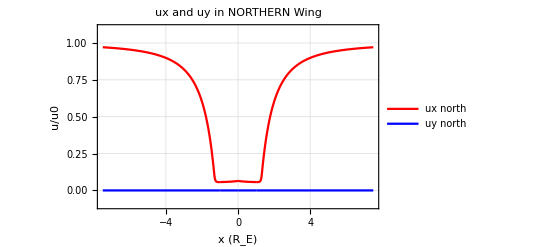

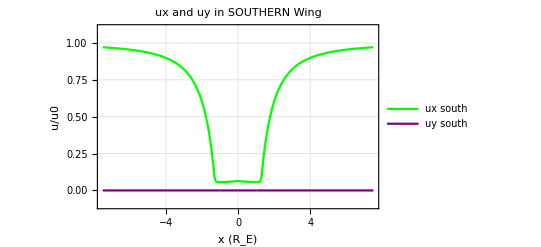

```mathematica
(*Validation: Plot components of flow field*)
uxnorthalongx[x_]=uxnorth[x,0]/u0; (*cut along x axis*)
uynorthalongx[x_]=uynorth[x,0]/u0;
uxsouthalongx[x_]=uxsouth[x,0]/u0;
uysouthalongx[x_]=uysouth[x,0]/u0;
Plot[{uxnorthalongx[x*RE],uynorthalongx[x*RE]},{x,-7.5,7.5},FrameLabel->{"x (R_E)","u/u0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"ux and uy in NORTHERN Wing", PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLegends ->{"ux north","uy north"},PlotRange->{-0.1,1.1}]
Plot[{uxsouthalongx[x*RE],uysouthalongx[x*RE]},{x,-7.5,7.5},FrameLabel->{"x (R_E)","u/u0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"ux and uy in SOUTHERN Wing", PlotStyle->{{Green,Thick},{Purple,Thick}},PlotLegends ->{"ux south","uy south"},PlotRange->{-0.1,1.1}]
```

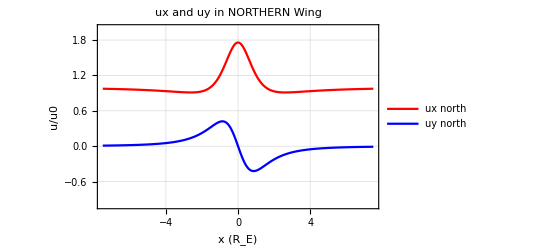

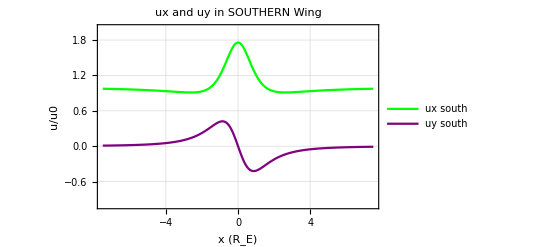

```mathematica
uxnorthshiftpos[x_]=uxnorth[x,1.5RE]/u0;(*cut at y=1.5 RE, i.e., displaced TOWARD Jupiter*)
uynorthshiftpos[x_]=uynorth[x,1.5RE]/u0;
uxsouthshiftpos[x_]=uxsouth[x,1.5RE]/u0;
uysouthshiftpos[x_]=uysouth[x,1.5RE]/u0;
Plot[{uxnorthshiftpos[x*RE],uynorthshiftpos[x*RE]},{x,-7.5,7.5},FrameLabel->{"x (R_E)","u/u0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"ux and uy in NORTHERN Wing", PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLegends ->{"ux north","uy north"},PlotRange->{-1,2}]
Plot[{uxsouthshiftpos[x*RE],uysouthshiftpos[x*RE]},{x,-7.5,7.5},FrameLabel->{"x (R_E)","u/u0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"ux and uy in SOUTHERN Wing", PlotStyle->{{Green,Thick},{Purple,Thick}},PlotLegends ->{"ux south","uy south"},PlotRange->{-1,2}]
```

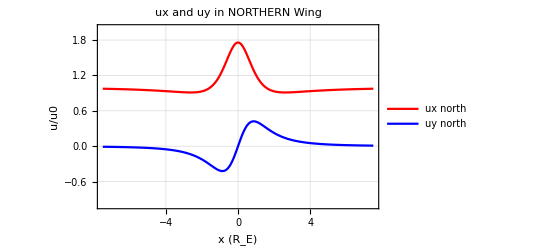

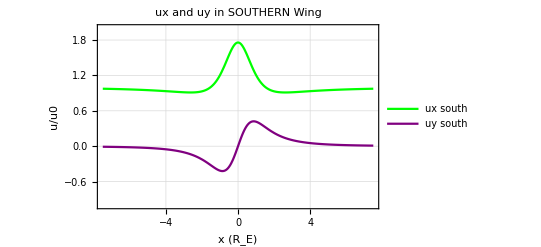

```mathematica
uxnorthshiftneg[x_]=uxnorth[x,-1.5RE]/u0; (*cut at y=-1.5 RE, i.e., displaced AWAY FROM Jupiter*)
uynorthshiftneg[x_]=uynorth[x,-1.5RE]/u0;
uxsouthshiftneg[x_]=uxsouth[x,-1.5RE]/u0;
uysouthshiftneg[x_]=uysouth[x,-1.5RE]/u0;
Plot[{uxnorthshiftneg[x*RE],uynorthshiftneg[x*RE]},{x,-7.5,7.5},FrameLabel->{"x (R_E)","u/u0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"ux and uy in NORTHERN Wing", PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLegends ->{"ux north","uy north"},PlotRange->{-1,2}]
Plot[{uxsouthshiftneg[x*RE],uysouthshiftneg[x*RE]},{x,-7.5,7.5},FrameLabel->{"x (R_E)","u/u0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"ux and uy in SOUTHERN Wing", PlotStyle->{{Green,Thick},{Purple,Thick}},PlotLegends ->{"ux south","uy south"},PlotRange->{-1,2}]
```

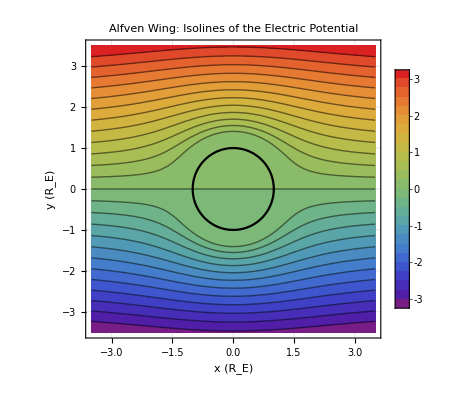

```mathematica
(*plot the flow field in both hemispheres. The electric field is perpendicular to the flow, and also to the isolines of the electric potential. So a visulaization of psi will do the job, as the psi=const lines are identical to the stream lines of u. For this plot the potential is normalized to the undisturbed electric potential E0 RE at the surface of Europa.*)
Plot1=ParametricPlot[{Cos[t],Sin[t]}, {t,0, 2*Pi}, AspectRatio->Automatic,AxesLabel->{"x (R_E)","y (R_E)"},PlotStyle->{Black,thick,solid}];
Plot2=ContourPlot[psi[x*RE,y*RE]/(E0*RE),{x,-3.5,3.5},{y,-3.5,3.5},Frame->True,GridLines->Automatic, FrameLabel->{"x (R_E)","y (R_E)"},Contours->25,ColorFunction->"Rainbow",PlotLegends->Automatic];
Plot3=Show[Plot2,Plot1,PlotLabel->"Alfven Wing: Isolines of the Electric Potential"]
```

```mathematica
(*-----------------------------------------------------------*)
(*12/04/2020: calculate surface flux of the thermal plasma flow along Europa's ramside. Radial unit vector: (+cos phi, +sin phi,0).  *)
(*-----------------------------------------------------------*)
(*first: confirm north-south symmetry of the flow deflection pattern*)
uxnorth[x,y]-uxsouth[x,y]//FullSimplify
uynorth[x,y]-uysouth[x,y]//FullSimplify
```

0.

0.

```mathematica
(*Surface NUMBER flux*)
flux[x_,y_]= Abs[n0*(cosphi[x,y]*uxnorth[x,y] + sinphi[x,y]*uynorth[x,y])];
(*flux along the equator*)
eqflux[y_]=flux[√(RE^2-y^2),y];
(*flux along a circle of radius lam(bda) RE*)
eqfluxabove[y_,lam_]=flux[√((lam *RE)^2-y^2),y];
(*standard "bullseye flux *)
bullseyeflux[x_,y_]=Abs[n0*u0*cosphi[x,y]];
(*bullseye flux along equator*)
eqbullseyeflux[y_]=bullseyeflux[√(RE^2-y^2),y];
(*bullseye flux along a circle of radius lam(bda) RE*)
eqbullseyefluxabove[y_,lam_]=bullseyeflux[√((lam*RE)^2-y^2),y];
```

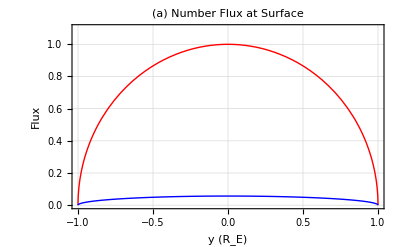

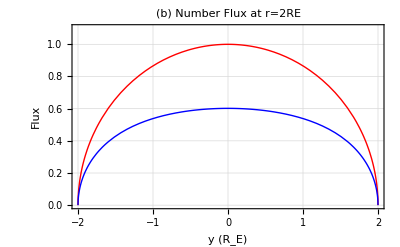

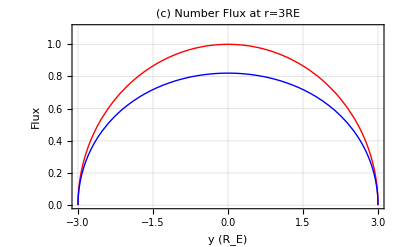

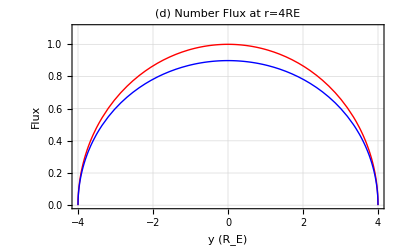

```mathematica
PlotA=Plot[{eqbullseyeflux[y*RE]/(n0*u0),eqflux[y*RE]/(n0*u0)},{y,-1,1},FrameLabel->{"y (R_E)","Flux"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(a) Number Flux at Surface", PlotStyle->{{Red,Thick},{Blue, Thick}},PlotRange->{0,1.1}]
PlotB=Plot[{eqbullseyefluxabove[y*RE,2]/(n0*u0),eqfluxabove[y*RE,2]/(n0*u0)},{y,-2,2},FrameLabel->{"y (R_E)","Flux"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(b) Number Flux at r=2RE", PlotStyle->{{Red,Thick},{Blue, Thick}},PlotRange->{0,1.1}]
PlotC=Plot[{eqbullseyefluxabove[y*RE,3]/(n0*u0),eqfluxabove[y*RE,3]/(n0*u0)},{y,-3,3},FrameLabel->{"y (R_E)","Flux"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(c) Number Flux at r=3RE", PlotStyle->{{Red,Thick},{Blue, Thick}},PlotRange->{0,1.1}]
PlotD=Plot[{eqbullseyefluxabove[y*RE,4]/(n0*u0),eqfluxabove[y*RE,4]/(n0*u0)},{y,-4,4},FrameLabel->{"y (R_E)","Flux"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(d) Number Flux at r=4RE", PlotStyle->{{Red,Thick},{Blue, Thick}},PlotRange->{0,1.1}]
```

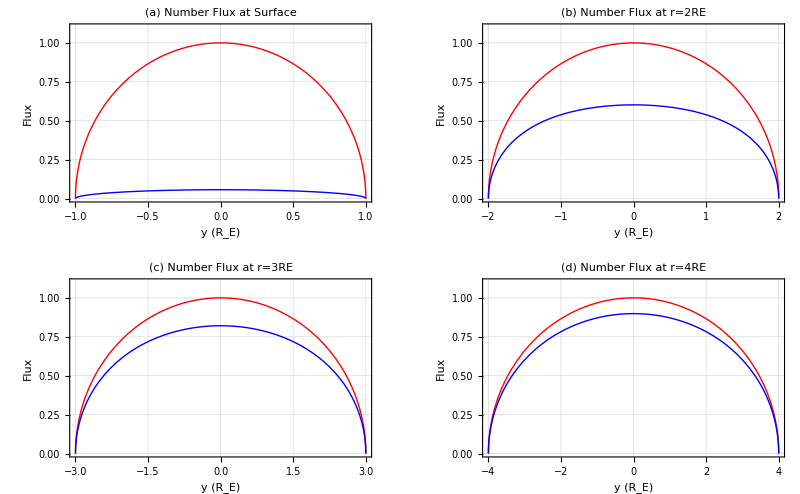

```mathematica
GraphicsGrid[{{PlotA,PlotB},{PlotC,PlotD}}]
```

```mathematica
(*now let's do the same for the ENERGY DEPOSITION, NOT FLUX*)
```

```mathematica
Edep[x_,y_]= Abs[n0*m/2*(uxnorth[x,y] *uxnorth[x,y] + uynorth[x,y]*uynorth[x,y]+ uznorth[x,y]*uznorth[x,y])];
(*deposition along the equator*)
Eeqdep[y_]=Edep[√(RE^2-y^2),y];
(*deposition along a circle of radius lam(bda) RE*)
Eeqdepabove[y_,lam_]=Edep[√((lam *RE)^2-y^2),y];
(*standard "bullseye deposition *)
Ebullseyedep[x_,y_]=Abs[n0*m*u0*u0/2];
(*bullseye deposition along equator*)
Eeqbullseyedep[y_]=Ebullseyedep[√(RE^2-y^2),y];
(*bullseye deposition along a circle of radius lam(bda) RE*)
Eeqbullseyedepabove[y_,lam_]=Ebullseyedep[√((lam*RE)^2-y^2),y];
```

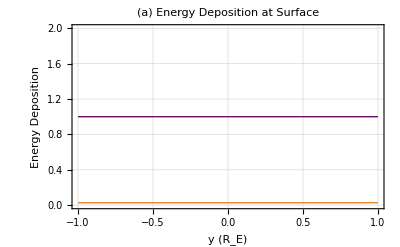

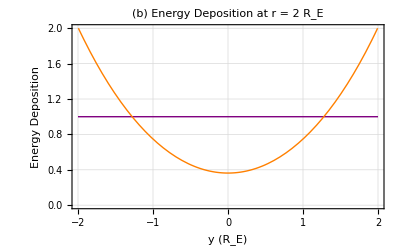

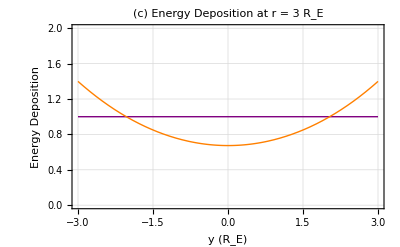

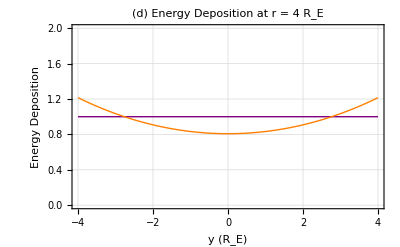

```mathematica
PlotE=Plot[{Eeqbullseyedep[y*RE]/(n0*m*u0*u0/2),Eeqdep[y*RE]/(n0*m*u0*u0/2)},{y,-1,1},FrameLabel->{"y (R_E)","Energy Deposition"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(a) Energy Deposition at Surface", PlotStyle->{{Purple,Thick},{Orange, Thick}},PlotRange->{0,2}]
PlotF=Plot[{Eeqbullseyedepabove[y*RE,2]/(n0*m*u0*u0/2),Eeqdepabove[y*RE,2]/(n0*m*u0*u0/2)},{y,-2,2},FrameLabel->{"y (R_E)","Energy Deposition"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(b) Energy Deposition at r = 2 R_E", PlotStyle->{{Purple,Thick},{Orange, Thick}},PlotRange->{0,2}]
PlotG=Plot[{Eeqbullseyedepabove[y*RE,3]/(n0*m*u0*u0/2),Eeqdepabove[y*RE,3]/(n0*m*u0*u0/2)},{y,-3,3},FrameLabel->{"y (R_E)","Energy Deposition"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(c) Energy Deposition at r = 3 R_E", PlotStyle->{{Purple,Thick},{Orange, Thick}},PlotRange->{0,2}]
PlotH=Plot[{Eeqbullseyedepabove[y*RE,4]/(n0*m*u0*u0/2),Eeqdepabove[y*RE,4]/(n0*m*u0*u0/2)},{y,-4,4},FrameLabel->{"y (R_E)","Energy Deposition"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(d) Energy Deposition at r = 4 R_E", PlotStyle->{{Purple,Thick},{Orange, Thick}},PlotRange->{0,2}]
```

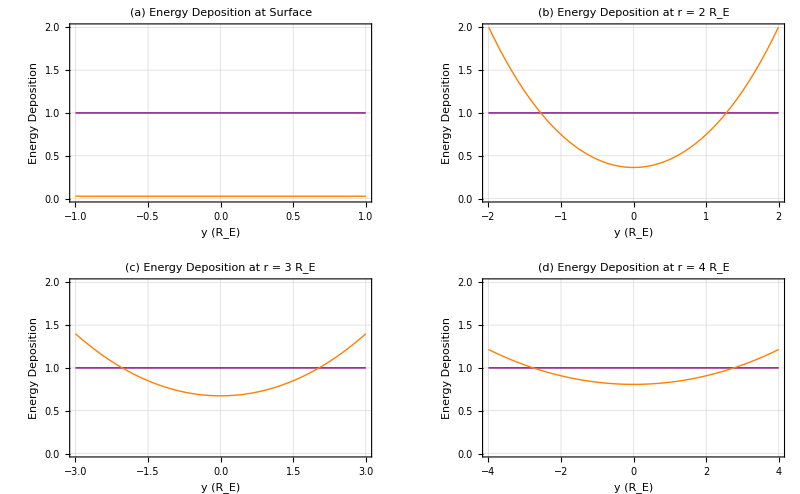

```mathematica
GraphicsGrid[{{PlotE,PlotF},{PlotG,PlotH}}]
```

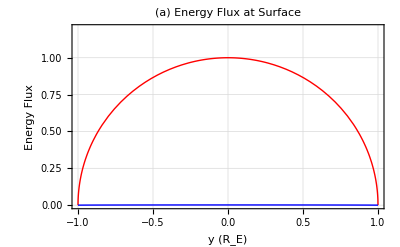

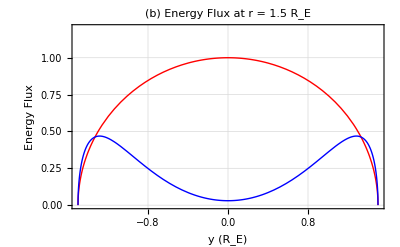

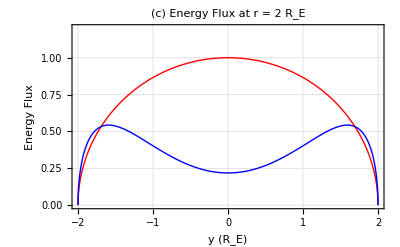

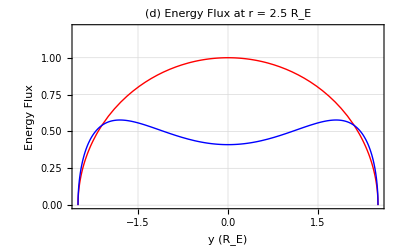

```mathematica
(*12/11/2020: Now let's do the actual energy flux! EFlux= 1/2 n m u^2 vec{u}* e_r, see plasma physics HW, sheet 4*)
Eflux[x_,y_]= Abs[n0*m/2*(uxnorth[x,y] *uxnorth[x,y] + uynorth[x,y]*uynorth[x,y]+ uznorth[x,y]*uznorth[x,y])*(cosphi[x,y]*uxnorth[x,y] + sinphi[x,y]*uynorth[x,y])];
(*deposition along the equator*)
Eeqflux[y_]=Eflux[√(RE^2-y^2),y];
(*deposition along a circle of radius lam(bda) RE*)
Eeqfluxabove[y_,lam_]=Eflux[√((lam *RE)^2-y^2),y];
(*standard "bullseye deposition *)
Ebullseyeflux[x_,y_]=Abs[n0*m*u0*u0*(cosphi[x,y]*u0)/2];
(*bullseye deposition along equator*)
Eeqbullseyeflux[y_]=Ebullseyeflux[√(RE^2-y^2),y];
(*bullseye deposition along a circle of radius lam(bda) RE*)
Eeqbullseyefluxabove[y_,lam_]=Ebullseyeflux[√((lam*RE)^2-y^2),y];
PlotFluxE=Plot[{Eeqbullseyeflux[y*RE]/(n0*m*u0*u0*u0/2),Eeqflux[y*RE]/(n0*m*u0*u0*u0/2)},{y,-1,1},FrameLabel->{"y (R_E)","Energy Flux"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(a) Energy Flux at Surface", PlotStyle->{{Red,Thick},{Blue, Thick}},PlotRange->{0,1.2}]
PlotFluxF=Plot[{Eeqbullseyefluxabove[y*RE, 1.5]/(n0*m*u0*u0*u0/2),Eeqfluxabove[y*RE,1.5]/(n0*m*u0*u0*u0/2)},{y,-1.5,1.5},FrameLabel->{"y (R_E)","Energy Flux"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(b) Energy Flux at r = 1.5 R_E", PlotStyle->{{Red,Thick},{Blue, Thick}},PlotRange->{0,1.2}]
PlotFluxG=Plot[{Eeqbullseyefluxabove[y*RE,2]/(n0*m*u0*u0*u0/2),Eeqfluxabove[y*RE,2]/(n0*m*u0*u0*u0/2)},{y,-2,2},FrameLabel->{"y (R_E)","Energy Flux"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(c) Energy Flux at r = 2 R_E", PlotStyle->{{Red,Thick},{Blue, Thick}},PlotRange->{0,1.2}]
PlotFluxH=Plot[{Eeqbullseyefluxabove[y*RE,2.5]/(n0*m*u0*u0*u0/2),Eeqfluxabove[y*RE,2.5]/(n0*m*u0*u0*u0/2)},{y,-2.5,2.5},FrameLabel->{"y (R_E)","Energy Flux"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(d) Energy Flux at r = 2.5 R_E", PlotStyle->{{Red,Thick},{Blue, Thick}},PlotRange->{0,1.2}]
```

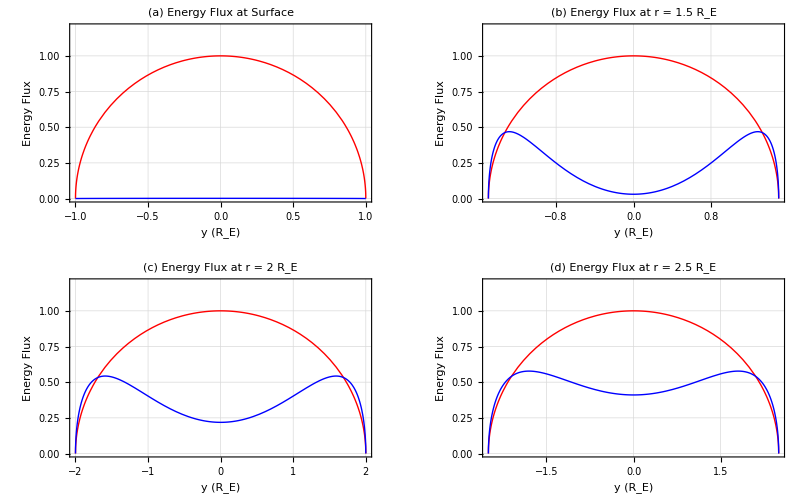

```mathematica
GraphicsGrid[{{PlotFluxE,PlotFluxF},{PlotFluxG,PlotFluxH}}]
```

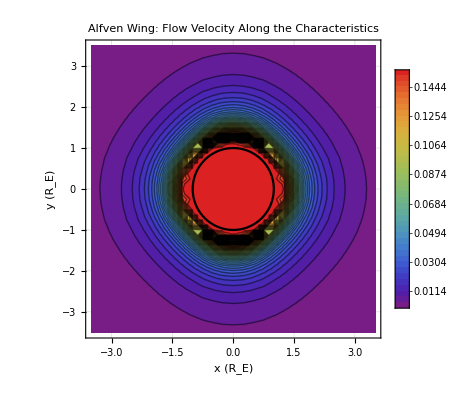

```mathematica
(*have a closer look at uz*)
Plot11=ParametricPlot[{Cos[t],Sin[t]}, {t,0, 2*Pi}, AspectRatio->Automatic,AxesLabel->{"x (R_E)","y (R_E)"},PlotStyle->{Black,thick,solid}];
Plot12=ContourPlot[uznorth[x*RE,y*RE]/(u0),{x,-3.5,3.5},{y,-3.5,3.5},Frame->True,GridLines->Automatic, FrameLabel->{"x (R_E)","y (R_E)"},Contours->40,ColorFunction->"Rainbow",PlotLegends->Automatic];
Plot13=Show[Plot12,Plot11,PlotLabel->"Alfven Wing: Flow Velocity Along the Characteristics"]
```

```mathematica
(*12/07/20: Currents along the Alfven wing characteristics, j = - sigmaA laplace psi*)
jpar1[x_,y_]= SigmaA * beta * sinphi[x,y]* K1*(1-Exp[-beta*r[x,y]]*(beta*r[x,y]+1))/(r[x,y]*r[x,y]); (*region 1: r ≤ R1*)
jpar2[x_,y_]=-SigmaA * delta * sinphi[x,y]*(K3+K4*Exp[delta*r[x,y]]*(delta*r[x,y]-1))/(r[x,y]*r[x,y]); (*region 2: R1 ≤r ≤ R2*)
jpar3[x_,y_]=0; (*region 3: R2 ≤ r*)
jpar[x_,y_]=Piecewise[{{SigmaA*beta* K1* beta^2/2,r[x,y]==0},{jpar1[x,y],0<r[x,y] ≤ R1},{jpar2[x,y],  R1 < r[x,y] ≤ R2},{jpar3[x,y], R2< r[x,y] }}];
```

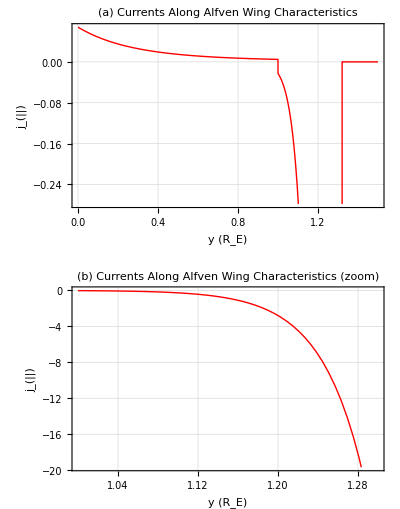

```mathematica
(*Plotting*)
jparalongy[y_]=jpar[0, y];
Plotcurr1=Plot[jparalongy[y*RE]/(SigmaA E0 /RE),{y,0,1.5}, FrameLabel->{"y (R_E)","j_(||)"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(a) Currents Along Alfven Wing Characteristics", PlotStyle->{Red,Thick}] ;
Plotcurr2=Plot[jparalongy[y*RE]/(SigmaA E0 /RE),{y,1.,1.3}, FrameLabel->{"y (R_E)","j_(||)"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(b) Currents Along Alfven Wing Characteristics (zoom)", PlotStyle->{Red,Thick}] ;
GraphicsGrid[{{Plotcurr1},{Plotcurr2}}]
```

```mathematica
(*How does this jump of Jparallel manifest in the magnetic field? NOTE: Bz has been detrended for the plot*)
```

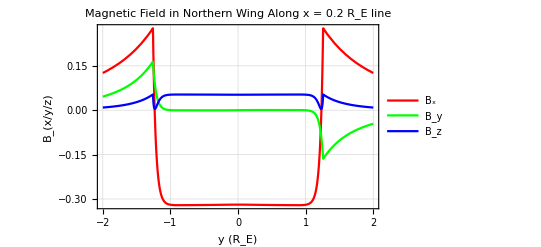

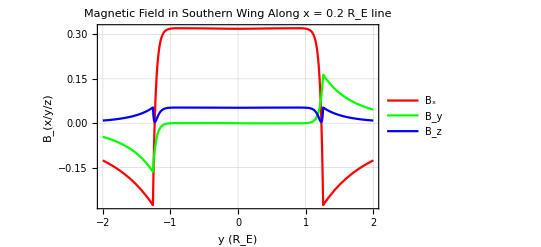

```mathematica
Plotmagnorth=Plot[{Bxnorth[0.4RE,y*RE]/(B0),Bynorth[0.4 RE,y*RE]/(B0),Bznorth[0.4 RE,y*RE]/(B0)+B0/B0},{y,-2.0,2.0}, FrameLabel->{"y (R_E)","B_(x/y/z)"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"Magnetic Field in Northern Wing Along x = 0.2 R_E line", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick}},PlotLegends ->{"B_x","B_y","B_z"}] 
Plotmagsouth=Plot[{Bxsouth[0.4RE,y*RE]/(B0),Bysouth[0.4 RE,y*RE]/(B0),Bzsouth[0.4 RE,y*RE]/(B0)+B0/B0},{y,-2.0,2.0}, FrameLabel->{"y (R_E)","B_(x/y/z)"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"Magnetic Field in Southern Wing Along x = 0.2 R_E line", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick}},PlotLegends ->{"B_x","B_y","B_z"}] 
(*GraphicsGrid[{{Plotmagnorth},{Plotmagsouth}}]*)
```

```mathematica
(*Poynting flux Sz along Alfven wing characteristics, wlog into northern hemisphere. Normalized to background flux u0 B0^2/mu0*)
Sz[x_,y_]=(dxpsi[x,y]*Bynorth[x,y]-(dypsi[x,y]-u0* Bznorth[x,y])*Bxnorth[x,y])/(u0*B0^2);
```

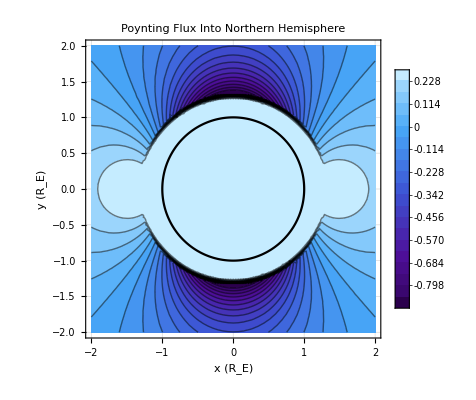

```mathematica
PlotS1=ParametricPlot[{Cos[t],Sin[t]}, {t,0, 2*Pi}, AspectRatio->Automatic,AxesLabel->{"x (R_E)","y (R_E)"},PlotStyle->{Black,thick,solid}];
PlotS2=ContourPlot[Sz[x*RE,y*RE],{x,-2.0,2.0},{y,-2.0,2.0},Frame->True,GridLines->Automatic, FrameLabel->{"x (R_E)","y (R_E)"},Contours->20,ColorFunction->"DeepSeaColors",PlotLegends->Automatic];
PlotS3=Show[PlotS2,PlotS1,PlotLabel->"Poynting Flux Into Northern Hemisphere"]
```

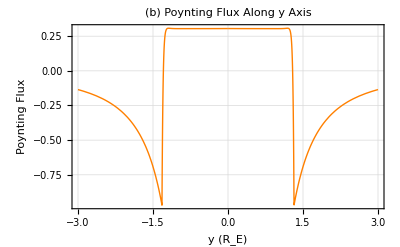

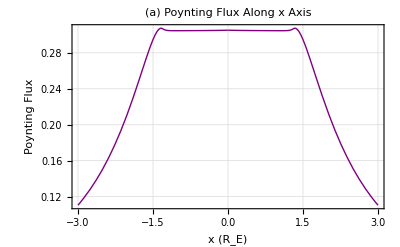

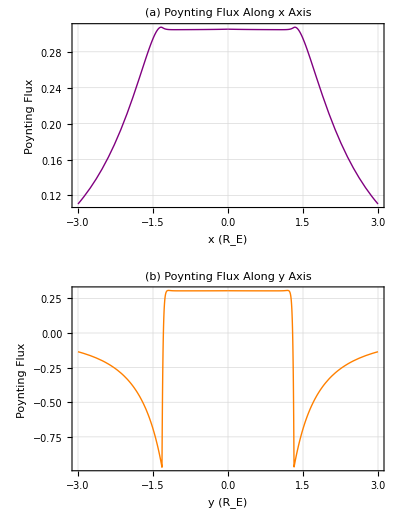

```mathematica
(*now: cut along y axis*)
PlotSalongx=Plot[Sz[0,y*RE],{y,-3,3}, FrameLabel->{"y (R_E)","Poynting Flux"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(b) Poynting Flux Along y Axis", PlotStyle->{Orange,Thick}] 
PlotSalongy=Plot[Sz[x*RE,0],{x,-3,3}, FrameLabel->{"x (R_E)","Poynting Flux"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(a) Poynting Flux Along x Axis", PlotStyle->{Purple,Thick}] 
GraphicsGrid[{{PlotSalongy},{PlotSalongx}}]
```